# Holder Test Plots

```mathematica
Clear[s0,jpc,flavor]
```

```mathematica
jpc="1--";
flavor="strange";
```

## Gaussian Sum-Rules - central

```mathematica
tag="central";
```

### QCD Parameters - central values

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.325,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Clear[mq,ms]
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
ms[μ_]=Module[{msat2=0.096},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.1349770,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.497611,fK->0.1562/(√2.)}
```

-0.0000774488

-0.00151037

```mathematica
αGG=0.075
```

0.075

```mathematica
M0=√0.8
```

0.894427

```mathematica
gggGGG=8.2 αGG
```

0.615

### Sum-Rules and Moments

```mathematica
Clear[gauss]
```

```mathematica
gauss[
k_Integer/;k≥0,
sHat_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
terms_:Table[1,{7}],
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=terms[[1]] Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]] Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=terms[[4]] Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=terms[[5]]Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=terms[[7]]*0* Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

1/(√(4π τ))Integrate[t^k Exp[(-(sHat-t)^2)/(4τ)](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[moment]
```

```mathematica
moment[
k_Integer/;k≥0,
0,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
1,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
2,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(t^2+2τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
3,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(t^2+6τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
n_Integer/;n≥4,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k 1/(√(4π τ))Integrate[sHat^n Exp[(-(sHat-t)^2)/(4τ)],{sHat,-∞,∞}](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[normalGauss,σSquared,Athree]
```

```mathematica
normalGauss[
k_Integer/;k≥0,
sHat_,τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
terms_:Table[1,{7}],
toggle_:0
]:=gauss[k,sHat,τ,s0,channel,type,terms,toggle]/moment[k,0,τ,s0,channel,type,toggle]
```

```mathematica
σSquared[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&)
]:=moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^2
```

```mathematica
Athree[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&)
]:=moment[k,3,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-3 moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type] moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]+2(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^3
```

### DNR Analysis

```mathematica
Clear[χSqMin,χSqMinData,s0optimized]
χSqMin[τ_Real,s0_Real]:=Module[
{sGrid,lhs,rhs,χSq,m1=2.188},

sGrid=Range[-10.,50.,0.25];
lhs=normalGauss[0,#,τ,s0,jpc,flavor]&/@sGrid;
rhs=1/(√(4π τ))(r Exp[-((#-m1^2)^2)/(4τ)]+(1-r)Exp[-((#-m2^2)^2)/(4τ)])&/@sGrid;
χSq=Total[(lhs-rhs)^2];
NMinimize[{χSq,r>=0,m2>0,r≤1.},{r,m2}]

]
χSqMinData=Flatten[Table[{τ,s0,χSqMin[τ,s0]},{τ,5.,20.,1.},{s0,5.,20.,0.1}],1];
χSqMinData>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"χSqMinData-"<>tag<>".m"
s0optimized=TakeSmallestBy[Cases[χSqMinData,{10.,s0_,χ_}:>{s0,χ[[1]]},{1}],Last,3][[1,1]]
s0optimized>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"s0optimized-"<>tag<>".m"
```

$Aborted

TakeSmallestBy::rank: The rank 3 is not an integer between 1 and 0.

Part::partw: Part 1 of {} does not exist.

TakeSmallestBy[{},Last,3]⟦1,1⟧

### Holder Definitions

```mathematica
G[s_,τ_,s0_,c_]=gauss[0,s,τ,s0,jpc,flavor,{1,1,1,1,1,1,1},c];
Gp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,1}]/.tau->τ;
Gpp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,2}]/.tau->τ;
```

```mathematica
h[s_,τ_,s0_,toggle_]=1-2*τ^2*(Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle])^2+2*τ*(2*Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle]+τ*Gpp[s,τ,s0,toggle]/G[s,τ,s0,toggle]);
```

### Plots

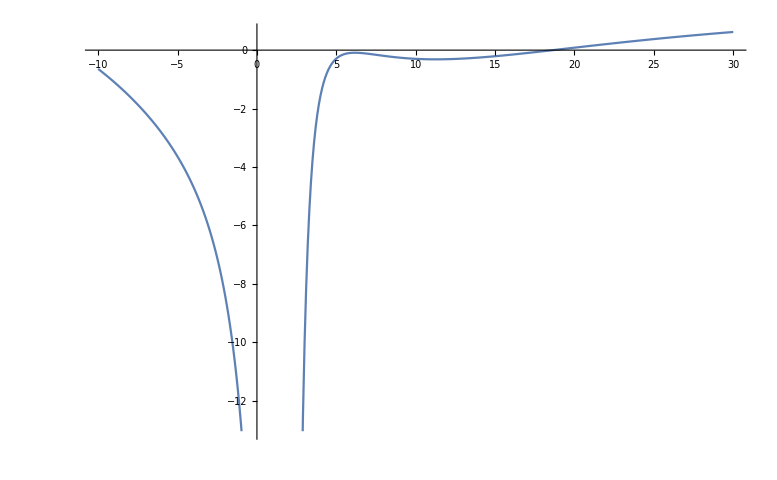

```mathematica
(*holderCoeffPlot=Plot[h[s,5,s0opt,coeff],h[s,10,s0opt,coeff],h[s,15,s0opt,coeff],h[s,20,s0opt,coeff],h[s,30,s0opt,coeff],h[s,40,s0opt,coeff]},{s,-10,30},PlotRange->{-0.1,0.30},PlotLegends->{"τ = 5","τ = 10","τ = 15","τ = 20","τ = 30","τ = 40"},AxesLabel->{"ŝ (GeV^2)",""},ImageSize->Large]
Export["holderPlot.pdf",holderCoeffPlot]*)
Clear[holderCoeffGrid,holderCoeffGridData]
holderCoeffGrid[τ_Real,s_Real]:=Module[
{sGrid,coeff,s0opt},
coeff = -1301/(240);
s0opt=s0optimized;
h[s,τ,s0opt,coeff]
]
holderCoeffGridData=Flatten[Table[{τ,s,holderCoeffGrid[τ,s]},{τ,5.,40.,1.},{s,-10.,30.,0.1}],1];
holderCoeffGridData>>NotebookDirectory[]<>"holderData-"<>tag<>".m"
ListLinePlot[Cases[holderCoeffGridData,{10.,s_,holder_}:>{s,holder},{1}]]
```

## Gaussian Sum-Rules - 3D

```mathematica
tag="3Dupper";
```

### QCD Parameters - 3D Upper Error

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.325,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Clear[mq,ms]
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
ms[μ_]=Module[{msat2=0.096},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.1349770+0.0000005,fpi->0.1304/(√2.)+0.0035}
mss=-0.5 MK^2 fK^2/.{MK->0.497611+0.000013,fK->0.1562/(√2.)+0.0042}
```

-0.0000834406

-0.0016275

```mathematica
αGG=0.075
```

0.075

```mathematica
M0=√0.8
```

0.894427

```mathematica
gggGGG=8.2 αGG
```

0.615

### Sum-Rules and Moments

```mathematica
Clear[gauss]
```

```mathematica
gauss[
k_Integer/;k≥0,
sHat_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
terms_:Table[1,{7}],
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=terms[[1]] Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]] Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=terms[[4]] Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=terms[[5]]Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=terms[[7]]*0* Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

1/(√(4π τ))Integrate[t^k Exp[(-(sHat-t)^2)/(4τ)](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[moment]
```

```mathematica
moment[
k_Integer/;k≥0,
0,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
1,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
2,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(t^2+2τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
3,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(t^2+6τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
n_Integer/;n≥4,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k 1/(√(4π τ))Integrate[sHat^n Exp[(-(sHat-t)^2)/(4τ)],{sHat,-∞,∞}](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[normalGauss,σSquared,Athree]
```

```mathematica
normalGauss[
k_Integer/;k≥0,
sHat_,τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=gauss[k,sHat,τ,s0,channel,type,toggle]/moment[k,0,τ,s0,channel,type,toggle]
```

```mathematica
σSquared[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&)
]:=moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^2
```

```mathematica
Athree[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&)
]:=moment[k,3,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-3 moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type] moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]+2(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^3
```

### DNR Analysis

```mathematica
Clear[χSqMin,χSqMinData,s0optimized]
χSqMin[τ_Real,s0_Real]:=Module[
{sGrid,lhs,rhs,χSq},

sGrid=Range[-10.,50.,0.25];
lhs=normalGauss[0,#,τ,s0,jpc,flavor]&/@sGrid;
rhs=1/(√(4π τ))(r Exp[-((#-m1^2)^2)/(4τ)]+(1-r)Exp[-((#-m2^2)^2)/(4τ)])&/@sGrid;
χSq=Total[(lhs-rhs)^2];
NMinimize[{χSq,1>r>0&&m1>0&&m2>0},{r,m1,m2}]

]
χSqMinData=Flatten[Table[{τ,s0,χSqMin[τ,s0]},{τ,5.,20.,1.},{s0,5.,20.,0.1}],1];
χSqMinData>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"χSqMinData-"<>tag<>".m"
s0optimized=TakeSmallestBy[Cases[χSqMinData,{10.,s0_,χ_}:>{s0,χ[[1]]},{1}],Last,3][[1,1]]
s0optimized>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"s0optimized-"<>tag<>".m"
```

### Holder Definitions

```mathematica
G[s_,τ_,s0_,c_]=gauss[0,s,τ,s0,jpc,flavor,{1,1,1,1,1,1,1},c];
Gp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,1}]/.tau->τ;
Gpp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,2}]/.tau->τ;
```

```mathematica
h[s_,τ_,s0_,toggle_]=1-2*τ^2*(Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle])^2+2*τ*(2*Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle]+τ*Gpp[s,τ,s0,toggle]/G[s,τ,s0,toggle]);
```

### Plots

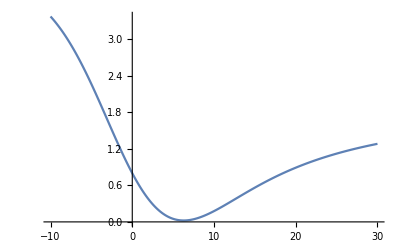

```mathematica
(*holderCoeffPlot=Plot[h[s,5,s0opt,coeff],h[s,10,s0opt,coeff],h[s,15,s0opt,coeff],h[s,20,s0opt,coeff],h[s,30,s0opt,coeff],h[s,40,s0opt,coeff]},{s,-10,30},PlotRange->{-0.1,0.30},PlotLegends->{"τ = 5","τ = 10","τ = 15","τ = 20","τ = 30","τ = 40"},AxesLabel->{"ŝ (GeV^2)",""},ImageSize->Large]
Export["holderPlot.pdf",holderCoeffPlot]*)
Clear[holderCoeffGrid,holderCoeffGridData]
holderCoeffGrid[τ_Real,s_Real]:=Module[
{sGrid,coeff,s0opt},
coeff = -1301/240;
s0opt=9.7;
h[s,τ,s0opt,coeff]
]
holderCoeffGridData=Flatten[Table[{τ,s,holderCoeffGrid[τ,s]},{τ,5.,40.,1.},{s,-10.,30.,0.1}],1];
holderCoeffGridData>>NotebookDirectory[]<>"holderData-"<>tag<>".m"
ListLinePlot[Cases[holderCoeffGridData,{10.,s_,holder_}:>{s,holder},{1}]]
```

```mathematica
tag="3Dlower";
```

### QCD Parameters - 3D Lower Error

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.325,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Clear[mq,ms]
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
ms[μ_]=Module[{msat2=0.096},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.1349770-0.0000005,fpi->0.1304/(√2.)-0.0035}
mss=-0.5 MK^2 fK^2/.{MK->0.497611-0.000013,fK->0.1562/(√2.)-0.0042}
```

-0.0000716802

-0.00139761

```mathematica
αGG=0.075
```

0.075

```mathematica
M0=√0.8
```

0.894427

```mathematica
gggGGG=8.2 αGG
```

0.615

### Sum-Rules and Moments

```mathematica
Clear[gauss]
```

```mathematica
gauss[
k_Integer/;k≥0,
sHat_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
terms_:Table[1,{7}],
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=terms[[1]] Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]] Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=terms[[4]] Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=terms[[5]]Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=terms[[7]]*0* Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

1/(√(4π τ))Integrate[t^k Exp[(-(sHat-t)^2)/(4τ)](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[moment]
```

```mathematica
moment[
k_Integer/;k≥0,
0,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
1,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
2,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(t^2+2τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
3,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(t^2+6τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
n_Integer/;n≥4,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k 1/(√(4π τ))Integrate[sHat^n Exp[(-(sHat-t)^2)/(4τ)],{sHat,-∞,∞}](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[normalGauss,σSquared,Athree]
```

```mathematica
normalGauss[
k_Integer/;k≥0,
sHat_,τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=gauss[k,sHat,τ,s0,channel,type,toggle]/moment[k,0,τ,s0,channel,type,toggle]
```

```mathematica
σSquared[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&)
]:=moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^2
```

```mathematica
Athree[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&)
]:=moment[k,3,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-3 moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type] moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]+2(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^3
```

### DNR Analysis

```mathematica
Clear[χSqMin,χSqMinData,s0optimized]
χSqMin[τ_Real,s0_Real]:=Module[
{sGrid,lhs,rhs,χSq},

sGrid=Range[-10.,50.,0.25];
lhs=normalGauss[0,#,τ,s0,jpc,flavor]&/@sGrid;
rhs=1/(√(4π τ))(r Exp[-((#-m1^2)^2)/(4τ)]+(1-r)Exp[-((#-m2^2)^2)/(4τ)])&/@sGrid;
χSq=Total[(lhs-rhs)^2];
NMinimize[{χSq,1>r>0&&m1>0&&m2>0},{r,m1,m2}]

]
χSqMinData=Flatten[Table[{τ,s0,χSqMin[τ,s0]},{τ,5.,20.,1.},{s0,5.,20.,0.1}],1];
χSqMinData>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"χSqMinData-"<>tag<>".m"
s0optimized=TakeSmallestBy[Cases[χSqMinData,{10.,s0_,χ_}:>{s0,χ[[1]]},{1}],Last,3][[1,1]]
s0optimized>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"s0optimized-"<>tag<>".m"
```

### Holder Definitions

```mathematica
G[s_,τ_,s0_,c_]=gauss[0,s,τ,s0,jpc,flavor,{1,1,1,1,1,1,1},c];
Gp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,1}]/.tau->τ;
Gpp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,2}]/.tau->τ;
```

```mathematica
h[s_,τ_,s0_,toggle_]=1-2*τ^2*(Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle])^2+2*τ*(2*Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle]+τ*Gpp[s,τ,s0,toggle]/G[s,τ,s0,toggle]);
```

### Plots

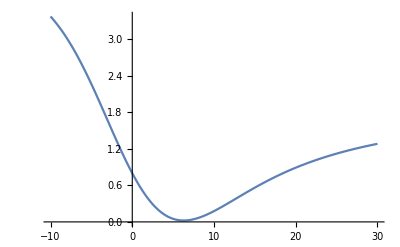

```mathematica
(*holderCoeffPlot=Plot[h[s,5,s0opt,coeff],h[s,10,s0opt,coeff],h[s,15,s0opt,coeff],h[s,20,s0opt,coeff],h[s,30,s0opt,coeff],h[s,40,s0opt,coeff]},{s,-10,30},PlotRange->{-0.1,0.30},PlotLegends->{"τ = 5","τ = 10","τ = 15","τ = 20","τ = 30","τ = 40"},AxesLabel->{"ŝ (GeV^2)",""},ImageSize->Large]
Export["holderPlot.pdf",holderCoeffPlot]*)
Clear[holderCoeffGrid,holderCoeffGridData]
holderCoeffGrid[τ_Real,s_Real]:=Module[
{sGrid,coeff,s0opt},
coeff = -1301/240;
s0opt=9.7;
h[s,τ,s0opt,coeff]
]
holderCoeffGridData=Flatten[Table[{τ,s,holderCoeffGrid[τ,s]},{τ,5.,40.,1.},{s,-10.,30.,0.1}],1];
holderCoeffGridData>>NotebookDirectory[]<>"holderData-"<>tag<>".m"
ListLinePlot[Cases[holderCoeffGridData,{10.,s_,holder_}:>{s,holder},{1}]]
```

## Gaussian Sum-Rules - 4D

```mathematica
tag="4Dupper";
```

### QCD Parameters - 4D Upper Error

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.325,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Clear[mq,ms]
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
ms[μ_]=Module[{msat2=0.096},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.1349770,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.497611,fK->0.1562/(√2.)}
```

-0.0000774488

-0.00151037

```mathematica
αGG=0.075+0.020
```

0.095

```mathematica
M0=√0.8
```

0.894427

```mathematica
gggGGG=8.2 αGG
```

0.779

### Sum-Rules and Moments

```mathematica
Clear[gauss]
```

```mathematica
gauss[
k_Integer/;k≥0,
sHat_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
terms_:Table[1,{7}],
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=terms[[1]] Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]] Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=terms[[4]] Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=terms[[5]]Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=terms[[7]]*0* Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

1/(√(4π τ))Integrate[t^k Exp[(-(sHat-t)^2)/(4τ)](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[moment]
```

```mathematica
moment[
k_Integer/;k≥0,
0,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
1,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
2,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(t^2+2τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
3,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(t^2+6τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
n_Integer/;n≥4,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k 1/(√(4π τ))Integrate[sHat^n Exp[(-(sHat-t)^2)/(4τ)],{sHat,-∞,∞}](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[normalGauss,σSquared,Athree]
```

```mathematica
normalGauss[
k_Integer/;k≥0,
sHat_,τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=gauss[k,sHat,τ,s0,channel,type,toggle]/moment[k,0,τ,s0,channel,type,toggle]
```

```mathematica
σSquared[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&)
]:=moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^2
```

```mathematica
Athree[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&)
]:=moment[k,3,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-3 moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type] moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]+2(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^3
```

### DNR Analysis

```mathematica
Clear[χSqMin,χSqMinData,s0optimized]
χSqMin[τ_Real,s0_Real]:=Module[
{sGrid,lhs,rhs,χSq},

sGrid=Range[-10.,50.,0.25];
lhs=normalGauss[0,#,τ,s0,jpc,flavor]&/@sGrid;
rhs=1/(√(4π τ))(r Exp[-((#-m1^2)^2)/(4τ)]+(1-r)Exp[-((#-m2^2)^2)/(4τ)])&/@sGrid;
χSq=Total[(lhs-rhs)^2];
NMinimize[{χSq,1>r>0&&m1>0&&m2>0},{r,m1,m2}]

]
χSqMinData=Flatten[Table[{τ,s0,χSqMin[τ,s0]},{τ,5.,20.,1.},{s0,5.,20.,0.1}],1];
χSqMinData>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"χSqMinData-"<>tag<>".m"
s0optimized=TakeSmallestBy[Cases[χSqMinData,{10.,s0_,χ_}:>{s0,χ[[1]]},{1}],Last,3][[1,1]]
s0optimized>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"s0optimized-"<>tag<>".m"
```

### Holder Definitions

```mathematica
G[s_,τ_,s0_,c_]=gauss[0,s,τ,s0,jpc,flavor,{1,1,1,1,1,1,1},c];
Gp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,1}]/.tau->τ;
Gpp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,2}]/.tau->τ;
```

```mathematica
h[s_,τ_,s0_,toggle_]=1-2*τ^2*(Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle])^2+2*τ*(2*Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle]+τ*Gpp[s,τ,s0,toggle]/G[s,τ,s0,toggle]);
```

### Plots

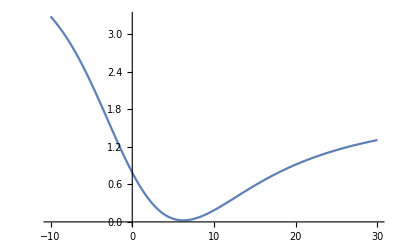

```mathematica
(*holderCoeffPlot=Plot[h[s,5,s0opt,coeff],h[s,10,s0opt,coeff],h[s,15,s0opt,coeff],h[s,20,s0opt,coeff],h[s,30,s0opt,coeff],h[s,40,s0opt,coeff]},{s,-10,30},PlotRange->{-0.1,0.30},PlotLegends->{"τ = 5","τ = 10","τ = 15","τ = 20","τ = 30","τ = 40"},AxesLabel->{"ŝ (GeV^2)",""},ImageSize->Large]
Export["holderPlot.pdf",holderCoeffPlot]*)
Clear[holderCoeffGrid,holderCoeffGridData]
holderCoeffGrid[τ_Real,s_Real]:=Module[
{sGrid,coeff,s0opt},
coeff = -1301/240;
s0opt=9.7;
h[s,τ,s0opt,coeff]
]
holderCoeffGridData=Flatten[Table[{τ,s,holderCoeffGrid[τ,s]},{τ,5.,40.,1.},{s,-10.,30.,0.1}],1];
holderCoeffGridData>>NotebookDirectory[]<>"holderData-"<>tag<>".m"
ListLinePlot[Cases[holderCoeffGridData,{10.,s_,holder_}:>{s,holder},{1}]]
```

```mathematica
tag="4Dlower";
```

### QCD Parameters - 4D Lower Error

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.325,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Clear[mq,ms]
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
ms[μ_]=Module[{msat2=0.096},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.1349770,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.497611,fK->0.1562/(√2.)}
```

-0.0000774488

-0.00151037

```mathematica
αGG=0.075-0.020
```

0.055

```mathematica
M0=√0.8
```

0.894427

```mathematica
gggGGG=8.2 αGG
```

0.451

### Sum-Rules and Moments

```mathematica
Clear[gauss]
```

```mathematica
gauss[
k_Integer/;k≥0,
sHat_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
terms_:Table[1,{7}],
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=terms[[1]] Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]] Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=terms[[4]] Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=terms[[5]]Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=terms[[7]]*0* Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

1/(√(4π τ))Integrate[t^k Exp[(-(sHat-t)^2)/(4τ)](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[moment]
```

```mathematica
moment[
k_Integer/;k≥0,
0,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
1,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
2,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(t^2+2τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
3,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(t^2+6τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
n_Integer/;n≥4,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k 1/(√(4π τ))Integrate[sHat^n Exp[(-(sHat-t)^2)/(4τ)],{sHat,-∞,∞}](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[normalGauss,σSquared,Athree]
```

```mathematica
normalGauss[
k_Integer/;k≥0,
sHat_,τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&),
toggle_:0
]:=gauss[k,sHat,τ,s0,channel,type,toggle]/moment[k,0,τ,s0,channel,type,toggle]
```

```mathematica
σSquared[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&)
]:=moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^2
```

```mathematica
Athree[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++",jpc,"1--"},#]&),
type_?(MemberQ[{flavor,"strange"},#]&)
]:=moment[k,3,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-3 moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type] moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]+2(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^3
```

### DNR Analysis

```mathematica
Clear[χSqMin,χSqMinData,s0optimized]
χSqMin[τ_Real,s0_Real]:=Module[
{sGrid,lhs,rhs,χSq},

sGrid=Range[-10.,50.,0.25];
lhs=normalGauss[0,#,τ,s0,jpc,flavor]&/@sGrid;
rhs=1/(√(4π τ))(r Exp[-((#-m1^2)^2)/(4τ)]+(1-r)Exp[-((#-m2^2)^2)/(4τ)])&/@sGrid;
χSq=Total[(lhs-rhs)^2];
NMinimize[{χSq,1>r>0&&m1>0&&m2>0},{r,m1,m2}]

]
χSqMinData=Flatten[Table[{τ,s0,χSqMin[τ,s0]},{τ,5.,20.,1.},{s0,5.,20.,0.1}],1];
χSqMinData>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"χSqMinData-"<>tag<>".m"
s0optimized=TakeSmallestBy[Cases[χSqMinData,{10.,s0_,χ_}:>{s0,χ[[1]]},{1}],Last,3][[1,1]]
s0optimized>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"s0optimized-"<>tag<>".m"
```

### Holder Definitions

```mathematica
G[s_,τ_,s0_,c_]=gauss[0,s,τ,s0,jpc,flavor,{1,1,1,1,1,1,1},c];
Gp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,1}]/.tau->τ;
Gpp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,2}]/.tau->τ;
```

```mathematica
h[s_,τ_,s0_,toggle_]=1-2*τ^2*(Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle])^2+2*τ*(2*Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle]+τ*Gpp[s,τ,s0,toggle]/G[s,τ,s0,toggle]);
```

### Plots

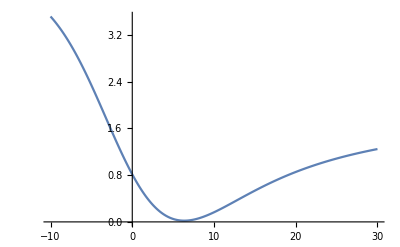

```mathematica
(*holderCoeffPlot=Plot[h[s,5,s0opt,coeff],h[s,10,s0opt,coeff],h[s,15,s0opt,coeff],h[s,20,s0opt,coeff],h[s,30,s0opt,coeff],h[s,40,s0opt,coeff]},{s,-10,30},PlotRange->{-0.1,0.30},PlotLegends->{"τ = 5","τ = 10","τ = 15","τ = 20","τ = 30","τ = 40"},AxesLabel->{"ŝ (GeV^2)",""},ImageSize->Large]
Export["holderPlot.pdf",holderCoeffPlot]*)
Clear[holderCoeffGrid,holderCoeffGridData]
holderCoeffGrid[τ_Real,s_Real]:=Module[
{sGrid,coeff,s0opt},
coeff = -1301/240;
s0opt=9.7;
h[s,τ,s0opt,coeff]
]
holderCoeffGridData=Flatten[Table[{τ,s,holderCoeffGrid[τ,s]},{τ,5.,40.,1.},{s,-10.,30.,0.1}],1];
holderCoeffGridData>>NotebookDirectory[]<>"holderData-"<>tag<>".m"
ListLinePlot[Cases[holderCoeffGridData,{10.,s_,holder_}:>{s,holder},{1}]]
```

## Gaussian Sum-Rules - 5D

```mathematica
tag="5Dupper";
```

### QCD Parameters - 5D Upper Error

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.325,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Clear[mq,ms]
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
ms[μ_]=Module[{msat2=0.096},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.1349770,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.497611,fK->0.1562/(√2.)}
```

-0.0000774488

-0.00151037

```mathematica
αGG=0.075
```

0.075

```mathematica
M0=√(0.8+0.1)
```

0.948683

```mathematica
gggGGG=8.2 αGG
```

0.615

### Sum-Rules and Moments

```mathematica
Clear[gauss]
```

```mathematica
gauss[
k_Integer/;k≥0,
sHat_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}],
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,flavor,mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,flavor,mqq,"strange",mss];
mgψσGψ=Switch[type,flavor,2 M0^2 mqq,"strange",2 M0^2 mss];
a=terms[[1]] Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]Switch[type,flavor,0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]] Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=terms[[4]] Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=terms[[5]]Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=terms[[7]]*0* Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

1/(√(4π τ))Integrate[t^k Exp[(-(sHat-t)^2)/(4τ)](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[moment]
```

```mathematica
moment[
k_Integer/;k≥0,
0,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
1,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
2,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(t^2+2τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
3,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),jpc,-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),jpc,1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),jpc,-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),jpc,-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,jpc,-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),jpc,5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(t^2+6τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
n_Integer/;n≥4,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k 1/(√(4π τ))Integrate[sHat^n Exp[(-(sHat-t)^2)/(4τ)],{sHat,-∞,∞}](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[normalGauss,σSquared,Athree]
```

```mathematica
normalGauss[
k_Integer/;k≥0,
sHat_,τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=gauss[k,sHat,τ,s0,channel,type,toggle]/moment[k,0,τ,s0,channel,type,toggle]
```

```mathematica
σSquared[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^2
```

```mathematica
Athree[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,3,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-3 moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type] moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]+2(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^3
```

### DNR Analysis

```mathematica
Clear[χSqMin,χSqMinData,s0optimized]
χSqMin[τ_Real,s0_Real]:=Module[
{sGrid,lhs,rhs,χSq},

sGrid=Range[-10.,50.,0.25];
lhs=normalGauss[0,#,τ,s0,jpc,flavor]&/@sGrid;
rhs=1/(√(4π τ))(r Exp[-((#-m1^2)^2)/(4τ)]+(1-r)Exp[-((#-m2^2)^2)/(4τ)])&/@sGrid;
χSq=Total[(lhs-rhs)^2];
NMinimize[{χSq,1>r>0&&m1>0&&m2>0},{r,m1,m2}]

]
χSqMinData=Flatten[Table[{τ,s0,χSqMin[τ,s0]},{τ,5.,20.,1.},{s0,5.,20.,0.1}],1];
χSqMinData>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"χSqMinData-"<>tag<>".m"
s0optimized=TakeSmallestBy[Cases[χSqMinData,{10.,s0_,χ_}:>{s0,χ[[1]]},{1}],Last,3][[1,1]]
s0optimized>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"s0optimized-"<>tag<>".m"
```

### Holder Definitions

```mathematica
G[s_,τ_,s0_,c_]=gauss[0,s,τ,s0,jpc,flavor,{1,1,1,1,1,1,1},c];
Gp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,1}]/.tau->τ;
Gpp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,2}]/.tau->τ;
```

```mathematica
h[s_,τ_,s0_,toggle_]=1-2*τ^2*(Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle])^2+2*τ*(2*Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle]+τ*Gpp[s,τ,s0,toggle]/G[s,τ,s0,toggle]);
```

### Plots

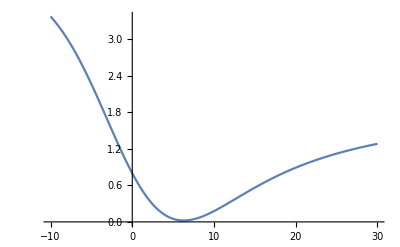

```mathematica
(*holderCoeffPlot=Plot[h[s,5,s0opt,coeff],h[s,10,s0opt,coeff],h[s,15,s0opt,coeff],h[s,20,s0opt,coeff],h[s,30,s0opt,coeff],h[s,40,s0opt,coeff]},{s,-10,30},PlotRange->{-0.1,0.30},PlotLegends->{"τ = 5","τ = 10","τ = 15","τ = 20","τ = 30","τ = 40"},AxesLabel->{"ŝ (GeV^2)",""},ImageSize->Large]
Export["holderPlot.pdf",holderCoeffPlot]*)
Clear[holderCoeffGrid,holderCoeffGridData]
holderCoeffGrid[τ_Real,s_Real]:=Module[
{sGrid,coeff,s0opt},
coeff = -1301/240;
s0opt=9.7;
h[s,τ,s0opt,coeff]
]
holderCoeffGridData=Flatten[Table[{τ,s,holderCoeffGrid[τ,s]},{τ,5.,40.,1.},{s,-10.,30.,0.1}],1];
holderCoeffGridData>>NotebookDirectory[]<>"holderData-"<>tag<>".m"
ListLinePlot[Cases[holderCoeffGridData,{10.,s_,holder_}:>{s,holder},{1}]]
```

```mathematica
tag="5Dlower";
```

### QCD Parameters - 5D Lower Error

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.325,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Clear[mq,ms]
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
ms[μ_]=Module[{msat2=0.096},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.1349770,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.497611,fK->0.1562/(√2.)}
```

-0.0000774488

-0.00151037

```mathematica
αGG=0.075
```

0.075

```mathematica
M0=√(0.8-0.1)
```

0.83666

```mathematica
gggGGG=8.2 αGG
```

0.615

### Sum-Rules and Moments

```mathematica
Clear[gauss]
```

```mathematica
gauss[
k_Integer/;k≥0,
sHat_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}],
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=terms[[1]] Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]] Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=terms[[4]] Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=terms[[5]]Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=terms[[7]]*0* Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

1/(√(4π τ))Integrate[t^k Exp[(-(sHat-t)^2)/(4τ)](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[moment]
```

```mathematica
moment[
k_Integer/;k≥0,
0,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
1,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
2,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(t^2+2τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
3,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(t^2+6τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
n_Integer/;n≥4,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k 1/(√(4π τ))Integrate[sHat^n Exp[(-(sHat-t)^2)/(4τ)],{sHat,-∞,∞}](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[normalGauss,σSquared,Athree]
```

```mathematica
normalGauss[
k_Integer/;k≥0,
sHat_,τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=gauss[k,sHat,τ,s0,channel,type,toggle]/moment[k,0,τ,s0,channel,type,toggle]
```

```mathematica
σSquared[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^2
```

```mathematica
Athree[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,3,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-3 moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type] moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]+2(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^3
```

### DNR Analysis

```mathematica
Clear[χSqMin,χSqMinData,s0optimized]
χSqMin[τ_Real,s0_Real]:=Module[
{sGrid,lhs,rhs,χSq},

sGrid=Range[-10.,50.,0.25];
lhs=normalGauss[0,#,τ,s0,jpc,flavor]&/@sGrid;
rhs=1/(√(4π τ))(r Exp[-((#-m1^2)^2)/(4τ)]+(1-r)Exp[-((#-m2^2)^2)/(4τ)])&/@sGrid;
χSq=Total[(lhs-rhs)^2];
NMinimize[{χSq,1>r>0&&m1>0&&m2>0},{r,m1,m2}]

]
χSqMinData=Flatten[Table[{τ,s0,χSqMin[τ,s0]},{τ,5.,20.,1.},{s0,5.,20.,0.1}],1];
χSqMinData>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"χSqMinData-"<>tag<>".m"
s0optimized=TakeSmallestBy[Cases[χSqMinData,{10.,s0_,χ_}:>{s0,χ[[1]]},{1}],Last,3][[1,1]]
s0optimized>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"s0optimized-"<>tag<>".m"
```

### Holder Definitions

```mathematica
G[s_,τ_,s0_,c_]=gauss[0,s,τ,s0,jpc,flavor,{1,1,1,1,1,1,1},c];
Gp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,1}]/.tau->τ;
Gpp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,2}]/.tau->τ;
```

```mathematica
h[s_,τ_,s0_,toggle_]=1-2*τ^2*(Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle])^2+2*τ*(2*Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle]+τ*Gpp[s,τ,s0,toggle]/G[s,τ,s0,toggle]);
```

### Plots

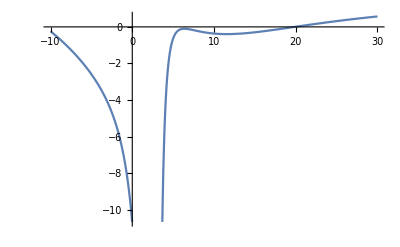

```mathematica
(*holderCoeffPlot=Plot[h[s,5,s0opt,coeff],h[s,10,s0opt,coeff],h[s,15,s0opt,coeff],h[s,20,s0opt,coeff],h[s,30,s0opt,coeff],h[s,40,s0opt,coeff]},{s,-10,30},PlotRange->{-0.1,0.30},PlotLegends->{"τ = 5","τ = 10","τ = 15","τ = 20","τ = 30","τ = 40"},AxesLabel->{"ŝ (GeV^2)",""},ImageSize->Large]
Export["holderPlot.pdf",holderCoeffPlot]*)
Clear[holderCoeffGrid,holderCoeffGridData]
holderCoeffGrid[τ_Real,s_Real]:=Module[
{sGrid,coeff,s0opt},
coeff = -1301/240;
s0opt=9.7;
h[s,τ,s0opt,coeff]
]
holderCoeffGridData=Flatten[Table[{τ,s,holderCoeffGrid[τ,s]},{τ,5.,40.,1.},{s,-10.,30.,0.1}],1];
holderCoeffGridData>>NotebookDirectory[]<>"holderData-"<>tag<>".m"
ListLinePlot[Cases[holderCoeffGridData,{10.,s_,holder_}:>{s,holder},{1}]]
```

## Gaussian Sum-Rules - α_s

```mathematica
tag="alphaupper";
```

### QCD Parameters - α_s Upper Error

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.325+0.015,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Clear[mq,ms]
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
ms[μ_]=Module[{msat2=0.096},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.1349770,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.497611,fK->0.1562/(√2.)}
```

-0.0000774488

-0.00151037

```mathematica
αGG=0.075
```

0.075

```mathematica
M0=√0.8
```

0.894427

```mathematica
gggGGG=8.2 αGG
```

0.615

### Sum-Rules and Moments

```mathematica
Clear[gauss]
```

```mathematica
gauss[
k_Integer/;k≥0,
sHat_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}],
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=terms[[1]] Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]] Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=terms[[4]] Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=terms[[5]]Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=terms[[7]]*0* Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

1/(√(4π τ))Integrate[t^k Exp[(-(sHat-t)^2)/(4τ)](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[moment]
```

```mathematica
moment[
k_Integer/;k≥0,
0,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
1,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
2,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(t^2+2τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
3,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(t^2+6τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
n_Integer/;n≥4,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k 1/(√(4π τ))Integrate[sHat^n Exp[(-(sHat-t)^2)/(4τ)],{sHat,-∞,∞}](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[normalGauss,σSquared,Athree]
```

```mathematica
normalGauss[
k_Integer/;k≥0,
sHat_,τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=gauss[k,sHat,τ,s0,channel,type,toggle]/moment[k,0,τ,s0,channel,type,toggle]
```

```mathematica
σSquared[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^2
```

```mathematica
Athree[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,3,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-3 moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type] moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]+2(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^3
```

### DNR Analysis

```mathematica
Clear[χSqMin,χSqMinData,s0optimized]
χSqMin[τ_Real,s0_Real]:=Module[
{sGrid,lhs,rhs,χSq},

sGrid=Range[-10.,50.,0.25];
lhs=normalGauss[0,#,τ,s0,jpc,flavor]&/@sGrid;
rhs=1/(√(4π τ))(r Exp[-((#-m1^2)^2)/(4τ)]+(1-r)Exp[-((#-m2^2)^2)/(4τ)])&/@sGrid;
χSq=Total[(lhs-rhs)^2];
NMinimize[{χSq,1>r>0&&m1>0&&m2>0},{r,m1,m2}]

]
χSqMinData=Flatten[Table[{τ,s0,χSqMin[τ,s0]},{τ,5.,20.,1.},{s0,5.,20.,0.1}],1];
χSqMinData>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"χSqMinData-"<>tag<>".m"
s0optimized=TakeSmallestBy[Cases[χSqMinData,{10.,s0_,χ_}:>{s0,χ[[1]]},{1}],Last,3][[1,1]]
s0optimized>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"s0optimized-"<>tag<>".m"
```

### Holder Definitions

```mathematica
G[s_,τ_,s0_,c_]=gauss[0,s,τ,s0,jpc,flavor,{1,1,1,1,1,1,1},c];
Gp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,1}]/.tau->τ;
Gpp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,2}]/.tau->τ;
```

```mathematica
h[s_,τ_,s0_,toggle_]=1-2*τ^2*(Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle])^2+2*τ*(2*Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle]+τ*Gpp[s,τ,s0,toggle]/G[s,τ,s0,toggle]);
```

### Plots

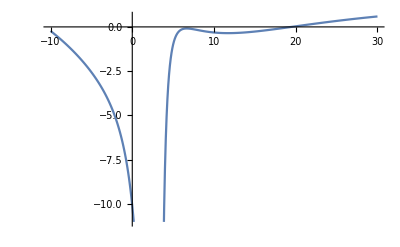

```mathematica
(*holderCoeffPlot=Plot[h[s,5,s0opt,coeff],h[s,10,s0opt,coeff],h[s,15,s0opt,coeff],h[s,20,s0opt,coeff],h[s,30,s0opt,coeff],h[s,40,s0opt,coeff]},{s,-10,30},PlotRange->{-0.1,0.30},PlotLegends->{"τ = 5","τ = 10","τ = 15","τ = 20","τ = 30","τ = 40"},AxesLabel->{"ŝ (GeV^2)",""},ImageSize->Large]
Export["holderPlot.pdf",holderCoeffPlot]*)
Clear[holderCoeffGrid,holderCoeffGridData]
holderCoeffGrid[τ_Real,s_Real]:=Module[
{sGrid,coeff,s0opt},
coeff = -1301/240;
s0opt=9.7;
h[s,τ,s0opt,coeff]
]
holderCoeffGridData=Flatten[Table[{τ,s,holderCoeffGrid[τ,s]},{τ,5.,40.,1.},{s,-10.,30.,0.1}],1];
holderCoeffGridData>>NotebookDirectory[]<>"holderData-"<>tag<>".m"
ListLinePlot[Cases[holderCoeffGridData,{10.,s_,holder_}:>{s,holder},{1}]]
```

```mathematica
tag="alphalower";
```

### QCD Parameters - α_s Lower Error

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.325-0.015,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Clear[mq,ms]
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
ms[μ_]=Module[{msat2=0.096},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.1349770,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.497611,fK->0.1562/(√2.)}
```

-0.0000774488

-0.00151037

```mathematica
αGG=0.075
```

0.075

```mathematica
M0=√0.8
```

0.894427

```mathematica
gggGGG=8.2 αGG
```

0.615

### Sum-Rules and Moments

```mathematica
Clear[gauss]
```

```mathematica
gauss[
k_Integer/;k≥0,
sHat_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}],
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=terms[[1]] Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]] Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=terms[[4]] Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=terms[[5]]Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=terms[[7]]*0* Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

1/(√(4π τ))Integrate[t^k Exp[(-(sHat-t)^2)/(4τ)](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[moment]
```

```mathematica
moment[
k_Integer/;k≥0,
0,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
1,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
2,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(t^2+2τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
3,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(t^2+6τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
n_Integer/;n≥4,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k 1/(√(4π τ))Integrate[sHat^n Exp[(-(sHat-t)^2)/(4τ)],{sHat,-∞,∞}](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[normalGauss,σSquared,Athree]
```

```mathematica
normalGauss[
k_Integer/;k≥0,
sHat_,τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=gauss[k,sHat,τ,s0,channel,type,toggle]/moment[k,0,τ,s0,channel,type,toggle]
```

```mathematica
σSquared[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^2
```

```mathematica
Athree[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,3,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-3 moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type] moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]+2(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^3
```

### DNR Analysis

```mathematica
Clear[χSqMin,χSqMinData,s0optimized]
χSqMin[τ_Real,s0_Real]:=Module[
{sGrid,lhs,rhs,χSq},

sGrid=Range[-10.,50.,0.25];
lhs=normalGauss[0,#,τ,s0,jpc,flavor]&/@sGrid;
rhs=1/(√(4π τ))(r Exp[-((#-m1^2)^2)/(4τ)]+(1-r)Exp[-((#-m2^2)^2)/(4τ)])&/@sGrid;
χSq=Total[(lhs-rhs)^2];
NMinimize[{χSq,1>r>0&&m1>0&&m2>0},{r,m1,m2}]

]
χSqMinData=Flatten[Table[{τ,s0,χSqMin[τ,s0]},{τ,5.,20.,1.},{s0,5.,20.,0.1}],1];
χSqMinData>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"χSqMinData-"<>tag<>".m"
s0optimized=TakeSmallestBy[Cases[χSqMinData,{10.,s0_,χ_}:>{s0,χ[[1]]},{1}],Last,3][[1,1]]
s0optimized>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"s0optimized-"<>tag<>".m"
```

### Holder Definitions

```mathematica
G[s_,τ_,s0_,c_]=gauss[0,s,τ,s0,jpc,flavor,{1,1,1,1,1,1,1},c];
Gp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,1}]/.tau->τ;
Gpp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,2}]/.tau->τ;
```

```mathematica
h[s_,τ_,s0_,toggle_]=1-2*τ^2*(Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle])^2+2*τ*(2*Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle]+τ*Gpp[s,τ,s0,toggle]/G[s,τ,s0,toggle]);
```

### Plots

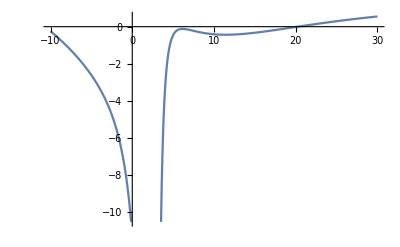

```mathematica
(*holderCoeffPlot=Plot[h[s,5,s0opt,coeff],h[s,10,s0opt,coeff],h[s,15,s0opt,coeff],h[s,20,s0opt,coeff],h[s,30,s0opt,coeff],h[s,40,s0opt,coeff]},{s,-10,30},PlotRange->{-0.1,0.30},PlotLegends->{"τ = 5","τ = 10","τ = 15","τ = 20","τ = 30","τ = 40"},AxesLabel->{"ŝ (GeV^2)",""},ImageSize->Large]
Export["holderPlot.pdf",holderCoeffPlot]*)
Clear[holderCoeffGrid,holderCoeffGridData]
holderCoeffGrid[τ_Real,s_Real]:=Module[
{sGrid,coeff,s0opt},
coeff = -1301/240;
s0opt=9.7;
h[s,τ,s0opt,coeff]
]
holderCoeffGridData=Flatten[Table[{τ,s,holderCoeffGrid[τ,s]},{τ,5.,40.,1.},{s,-10.,30.,0.1}],1];
holderCoeffGridData>>NotebookDirectory[]<>"holderData-"<>tag<>".m"
ListLinePlot[Cases[holderCoeffGridData,{10.,s_,holder_}:>{s,holder},{1}]]
```

## Gaussian Sum-Rules - s_0^opt

```mathematica
tag="s0upper";
```

### QCD Parameters - central values

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.325,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Clear[mq,ms]
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
ms[μ_]=Module[{msat2=0.096},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.1349770,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.497611,fK->0.1562/(√2.)}
```

-0.0000774488

-0.00151037

```mathematica
αGG=0.075
```

0.075

```mathematica
M0=√0.8
```

0.894427

```mathematica
gggGGG=8.2 αGG
```

0.615

### Sum-Rules and Moments

```mathematica
Clear[gauss]
```

```mathematica
gauss[
k_Integer/;k≥0,
sHat_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}],
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=terms[[1]] Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]] Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=terms[[4]] Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=terms[[5]]Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=terms[[7]]*0* Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

1/(√(4π τ))Integrate[t^k Exp[(-(sHat-t)^2)/(4τ)](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[moment]
```

```mathematica
moment[
k_Integer/;k≥0,
0,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
1,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
2,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(t^2+2τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
3,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(t^2+6τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
n_Integer/;n≥4,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k 1/(√(4π τ))Integrate[sHat^n Exp[(-(sHat-t)^2)/(4τ)],{sHat,-∞,∞}](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[normalGauss,σSquared,Athree]
```

```mathematica
normalGauss[
k_Integer/;k≥0,
sHat_,τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=gauss[k,sHat,τ,s0,channel,type,toggle]/moment[k,0,τ,s0,channel,type,toggle]
```

```mathematica
σSquared[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^2
```

```mathematica
Athree[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,3,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-3 moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type] moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]+2(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^3
```

### DNR Analysis

```mathematica
Clear[χSqMin,χSqMinData,s0optimized]
χSqMin[τ_Real,s0_Real]:=Module[
{sGrid,lhs,rhs,χSq},

sGrid=Range[-10.,50.,0.25];
lhs=normalGauss[0,#,τ,s0,jpc,flavor]&/@sGrid;
rhs=1/(√(4π τ))(r Exp[-((#-m1^2)^2)/(4τ)]+(1-r)Exp[-((#-m2^2)^2)/(4τ)])&/@sGrid;
χSq=Total[(lhs-rhs)^2];
NMinimize[{χSq,1>r>0&&m1>0&&m2>0},{r,m1,m2}]

]
χSqMinData=Flatten[Table[{τ,s0,χSqMin[τ,s0]},{τ,5.,20.,1.},{s0,5.,20.,0.1}],1];
χSqMinData>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"χSqMinData-"<>tag<>".m"
s0optimized=TakeSmallestBy[Cases[χSqMinData,{10.,s0_,χ_}:>{s0,χ[[1]]},{1}],Last,3][[1,1]]
s0optimized>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"s0optimized-"<>tag<>".m"
```

### Holder Definitions

```mathematica
G[s_,τ_,s0_,c_]=gauss[0,s,τ,s0,jpc,flavor,{1,1,1,1,1,1,1},c];
Gp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,1}]/.tau->τ;
Gpp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,2}]/.tau->τ;
```

```mathematica
h[s_,τ_,s0_,toggle_]=1-2*τ^2*(Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle])^2+2*τ*(2*Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle]+τ*Gpp[s,τ,s0,toggle]/G[s,τ,s0,toggle]);
```

### Plots

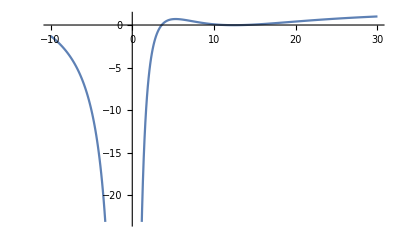

```mathematica
(*holderCoeffPlot=Plot[h[s,5,s0opt,coeff],h[s,10,s0opt,coeff],h[s,15,s0opt,coeff],h[s,20,s0opt,coeff],h[s,30,s0opt,coeff],h[s,40,s0opt,coeff]},{s,-10,30},PlotRange->{-0.1,0.30},PlotLegends->{"τ = 5","τ = 10","τ = 15","τ = 20","τ = 30","τ = 40"},AxesLabel->{"ŝ (GeV^2)",""},ImageSize->Large]
Export["holderPlot.pdf",holderCoeffPlot]*)
Clear[holderCoeffGrid,holderCoeffGridData]
holderCoeffGrid[τ_Real,s_Real]:=Module[
{sGrid,coeff,s0opt},
coeff = -1301/240;
s0opt=9.7+1.2;
h[s,τ,s0opt,coeff]
]
holderCoeffGridData=Flatten[Table[{τ,s,holderCoeffGrid[τ,s]},{τ,5.,40.,1.},{s,-10.,30.,0.1}],1];
holderCoeffGridData>>NotebookDirectory[]<>"holderData-"<>tag<>".m"
ListLinePlot[Cases[holderCoeffGridData,{10.,s_,holder_}:>{s,holder},{1}]]
```

```mathematica
tag="s0lower";
```

### QCD Parameters - central values

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.325,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Clear[mq,ms]
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
ms[μ_]=Module[{msat2=0.096},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.1349770,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.497611,fK->0.1562/(√2.)}
```

-0.0000774488

-0.00151037

```mathematica
αGG=0.075
```

0.075

```mathematica
M0=√0.8
```

0.894427

```mathematica
gggGGG=8.2 αGG
```

0.615

### Sum-Rules and Moments

```mathematica
Clear[gauss]
```

```mathematica
gauss[
k_Integer/;k≥0,
sHat_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}],
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=terms[[1]] Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]] Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=terms[[4]] Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=terms[[5]]Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=terms[[7]]*0* Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

1/(√(4π τ))Integrate[t^k Exp[(-(sHat-t)^2)/(4τ)](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[moment]
```

```mathematica
moment[
k_Integer/;k≥0,
0,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
1,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
2,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k(t^2+2τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
3,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^(k+1)(t^2+6τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
n_Integer/;n≥4,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)](1+toggle*α[τ^(1/4)]/π),m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

NIntegrate[t^k 1/(√(4π τ))Integrate[sHat^n Exp[(-(sHat-t)^2)/(4τ)],{sHat,-∞,∞}](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[normalGauss,σSquared,Athree]
```

```mathematica
normalGauss[
k_Integer/;k≥0,
sHat_,τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
toggle_:0
]:=gauss[k,sHat,τ,s0,channel,type,toggle]/moment[k,0,τ,s0,channel,type,toggle]
```

```mathematica
σSquared[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^2
```

```mathematica
Athree[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,3,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-3 moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type] moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]+2(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^3
```

### DNR Analysis

```mathematica
Clear[χSqMin,χSqMinData,s0optimized]
χSqMin[τ_Real,s0_Real]:=Module[
{sGrid,lhs,rhs,χSq},

sGrid=Range[-10.,50.,0.25];
lhs=normalGauss[0,#,τ,s0,jpc,flavor]&/@sGrid;
rhs=1/(√(4π τ))(r Exp[-((#-m1^2)^2)/(4τ)]+(1-r)Exp[-((#-m2^2)^2)/(4τ)])&/@sGrid;
χSq=Total[(lhs-rhs)^2];
NMinimize[{χSq,1>r>0&&m1>0&&m2>0},{r,m1,m2}]

]
χSqMinData=Flatten[Table[{τ,s0,χSqMin[τ,s0]},{τ,5.,20.,1.},{s0,5.,20.,0.1}],1];
χSqMinData>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"χSqMinData-"<>tag<>".m"
s0optimized=TakeSmallestBy[Cases[χSqMinData,{10.,s0_,χ_}:>{s0,χ[[1]]},{1}],Last,3][[1,1]]
s0optimized>>NotebookDirectory[]<>DateString["ISODate"]<>"-"<>"s0optimized-"<>tag<>".m"
```

### Holder Definitions

```mathematica
G[s_,τ_,s0_,c_]=gauss[0,s,τ,s0,jpc,flavor,{1,1,1,1,1,1,1},c];
Gp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,1}]/.tau->τ;
Gpp[s_,τ_,s0_,c_]=D[gauss[0,s,tau,s0,jpc,flavor,{1,1,1,1,1,1,1},c],{tau,2}]/.tau->τ;
```

```mathematica
h[s_,τ_,s0_,toggle_]=1-2*τ^2*(Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle])^2+2*τ*(2*Gp[s,τ,s0,toggle]/G[s,τ,s0,toggle]+τ*Gpp[s,τ,s0,toggle]/G[s,τ,s0,toggle]);
```

### Plots

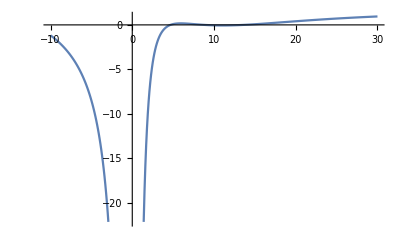

```mathematica
(*holderCoeffPlot=Plot[h[s,5,s0opt,coeff],h[s,10,s0opt,coeff],h[s,15,s0opt,coeff],h[s,20,s0opt,coeff],h[s,30,s0opt,coeff],h[s,40,s0opt,coeff]},{s,-10,30},PlotRange->{-0.1,0.30},PlotLegends->{"τ = 5","τ = 10","τ = 15","τ = 20","τ = 30","τ = 40"},AxesLabel->{"ŝ (GeV^2)",""},ImageSize->Large]
Export["holderPlot.pdf",holderCoeffPlot]*)
Clear[holderCoeffGrid,holderCoeffGridData]
holderCoeffGrid[τ_Real,s_Real]:=Module[
{sGrid,coeff,s0opt},
coeff = -1301/240;
s0opt=9.7-1.2;
h[s,τ,s0opt,coeff]
]
holderCoeffGridData=Flatten[Table[{τ,s,holderCoeffGrid[τ,s]},{τ,5.,40.,1.},{s,-10.,30.,0.1}],1];
holderCoeffGridData>>NotebookDirectory[]<>"holderData-"<>tag<>".m"
ListLinePlot[Cases[holderCoeffGridData,{10.,s_,holder_}:>{s,holder},{1}]]
```

## Plots

```mathematica
NotebookDirectory[]
```

/home/hojasonn/Documents/ResearchProjects/GSR-Y(2175)/

```mathematica
central=Get[(NotebookDirectory[]<>"holderData-"<>"central"<>".m")];
upper3d=Get[(NotebookDirectory[]<>"holderData-"<>"3Dupper"<>".m")];
lower3d=Get[(NotebookDirectory[]<>"holderData-"<>"3Dlower"<>".m")];
upper4d=Get[(NotebookDirectory[]<>"holderData-"<>"4Dupper"<>".m")];
lower4d=Get[(NotebookDirectory[]<>"holderData-"<>"4Dlower"<>".m")];
upper5d=Get[(NotebookDirectory[]<>"holderData-"<>"5Dupper"<>".m")];
lower5d=Get[(NotebookDirectory[]<>"holderData-"<>"5Dlower"<>".m")];
upperα=Get[(NotebookDirectory[]<>"holderData-"<>"alphaupper"<>".m")];
lowerα=Get[(NotebookDirectory[]<>"holderData-"<>"alphalower"<>".m")];
uppers0=Get[(NotebookDirectory[]<>"holderData-"<>"s0upper"<>".m")];
lowers0=Get[(NotebookDirectory[]<>"holderData-"<>"s0lower"<>".m")];
```

```mathematica
holderError[list_,τ_]:=Table[{Cases[list,{τ,s_,holder_}:>{s,holder},{1}][[i,1]],-Cases[list,{τ,s_,holder_}:>{s,holder},{1}][[i,2]]+Cases[central,{τ,s_,holder_}:>{s,holder},{1}][[i,2]]},{i,1,401,4}]
totalError[τ_]:=Sqrt[(holderError[upper3d,τ][[#,2]])^2+(holderError[lower4d,τ][[#,2]])^2+(holderError[upper5d,τ][[#,2]])^2+(holderError[lowerα,τ][[#,2]])^2+(holderError[lowers0,τ][[#,2]])^2]&/@Range[1,101]
```

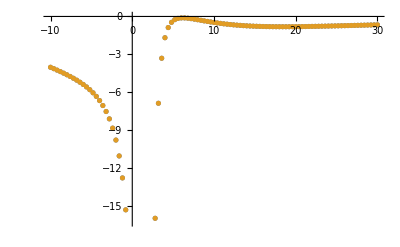

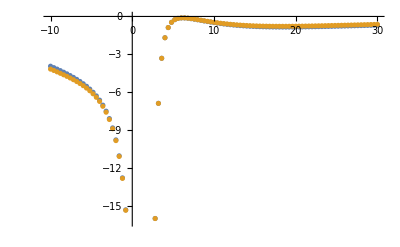

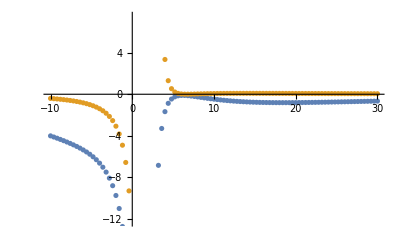

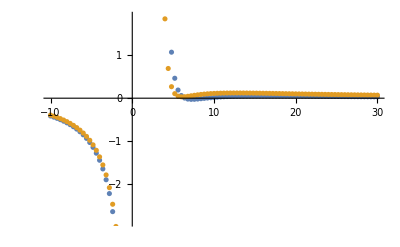

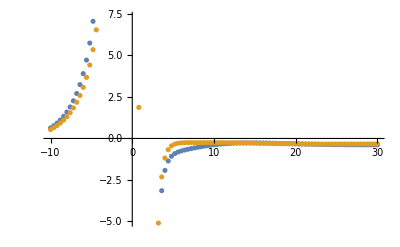

```mathematica
ListPlot[{holderError[upper3d,10.],holderError[lower3d,10.]}]
ListPlot[{holderError[upper4d,10.],holderError[lower4d,10.]}]
ListPlot[{holderError[upper5d,10.],holderError[lower5d,10.]}]
ListPlot[{holderError[upperα,10.],holderError[lowerα,10.]}]
ListPlot[{holderError[uppers0,10.],holderError[lowers0,10.]}]
```

```mathematica
Needs["ErrorBarPlots`"]
holderplot=ErrorListPlot[
{
Thread[{Cases[central,{10.,s_,holder_}:>{s,holder},{1}],ErrorBar/@totalError[10.]}]
}
]
```

$Aborted

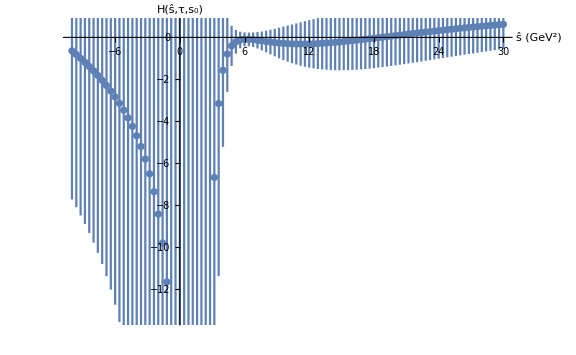

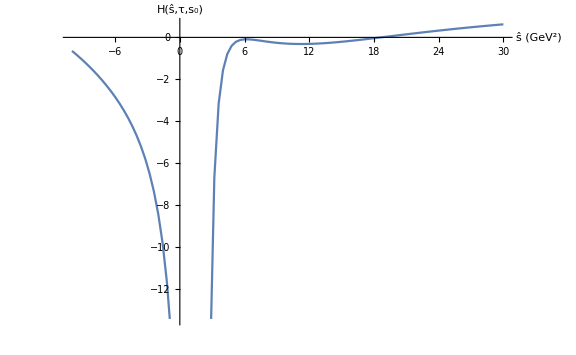

```mathematica
Clear[tauvalue,errbars,plotpoints]
tauvalue=10.;
errbars=totalError[tauvalue];
plotpoints=Table[Cases[central,{tauvalue,s_,holder_}:>{s,holder},{1}][[i]],{i,1,401,4}];
Table[Append[plotpoints[[i]],errbars[[i]]],{i,1,101}];
errors=ErrorListPlot[{
Flatten[Thread[{Cases[%,{s_,holder_,error_}:>{{s,holder},ErrorBar[error]},{1}]}],1]
},AxesLabel->{"ŝ (GeV^2)","H(ŝ,τ,s_0)"},ImageSize->Large(*,PlotRange->{0.5,0}*)]
plot=ListLinePlot[plotpoints
,AxesLabel->{"ŝ (GeV^2)","H(ŝ,τ,s_0)"},ImageSize->Large(*,PlotRange->{0.5,0}*)]
```

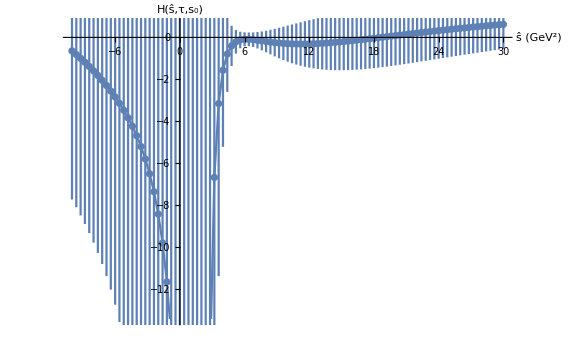

holder-tau10-errorbars.pdf

```mathematica
Show[plot, errors]
Export["holder-tau10-errorbars.pdf",%]
```

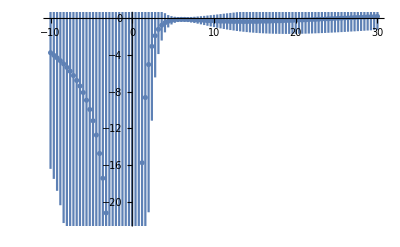

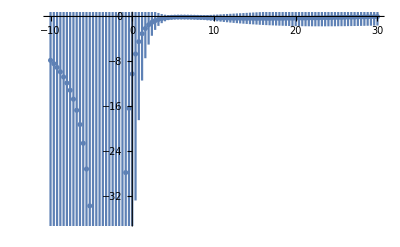

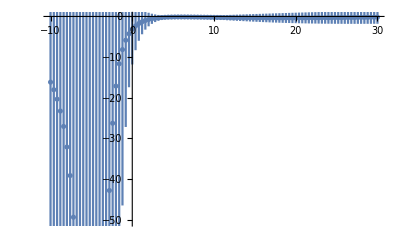

```mathematica
Clear[tauvalue,errbars,plotpoints]
tauvalue=15.;
errbars=totalError[tauvalue];
plotpoints=Table[Cases[central,{tauvalue,s_,holder_}:>{s,holder},{1}][[i]],{i,1,401,4}];
Table[Append[plotpoints[[i]],errbars[[i]]],{i,1,101}];
ErrorListPlot[{
Flatten[Thread[{Cases[%,{s_,holder_,error_}:>{{s,holder},ErrorBar[error]},{1}]}],1]
}]
Clear[tauvalue,errbars,plotpoints]
tauvalue=20.;
errbars=totalError[tauvalue];
plotpoints=Table[Cases[central,{tauvalue,s_,holder_}:>{s,holder},{1}][[i]],{i,1,401,4}];
Table[Append[plotpoints[[i]],errbars[[i]]],{i,1,101}];
ErrorListPlot[{
Flatten[Thread[{Cases[%,{s_,holder_,error_}:>{{s,holder},ErrorBar[error]},{1}]}],1]
}]
Clear[tauvalue,errbars,plotpoints]
tauvalue=25.;
errbars=totalError[tauvalue];
plotpoints=Table[Cases[central,{tauvalue,s_,holder_}:>{s,holder},{1}][[i]],{i,1,401,4}];
Table[Append[plotpoints[[i]],errbars[[i]]],{i,1,101}];
ErrorListPlot[{
Flatten[Thread[{Cases[%,{s_,holder_,error_}:>{{s,holder},ErrorBar[error]},{1}]}],1]
}]
```

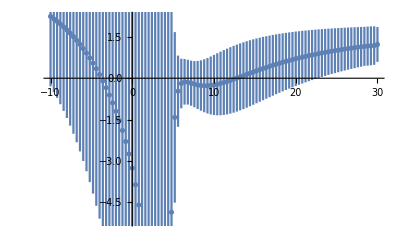

```mathematica
Clear[tauvalue,errbars,plotpoints]
tauvalue=5.;
errbars=totalError[tauvalue];
plotpoints=Table[Cases[central,{tauvalue,s_,holder_}:>{s,holder},{1}][[i]],{i,1,401,4}];
Table[Append[plotpoints[[i]],errbars[[i]]],{i,1,101}];
ErrorListPlot[{
Flatten[Thread[{Cases[%,{s_,holder_,error_}:>{{s,holder},ErrorBar[error]},{1}]}],1]
}]
```